```mathematica
zmin = 60
```

60

```mathematica
zmax = 200
```

200

```mathematica
200
r0 = 1
```

200

0.1

```mathematica
risk[z_] = (1 - (z - zmin) ^ 2 / (r0 * (zmax - zmin)) ^ 2)
```

1-0.00510204 (-60+z)^2

```mathematica
sq[z_] = zmin ^ 2  / z ^ 2
```

3600/z^2

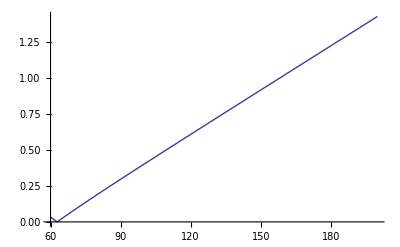

```mathematica
Plot[Abs[risk'[z]- sq'[z]], {z, zmin,zmax}]
```

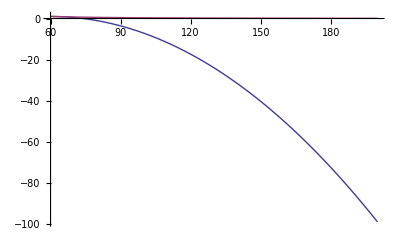

```mathematica
Plot[{risk[z],sq[z]},{z,zmin,zmax}]
```